```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xiaonuxiong/Nustore Files/Nutstore/PDF Euclidean Lattice/Hadron_Structure_Lattice/had_spec

```mathematica
π2ptTag=Import["..//PDF//pion_proton_PDF//pion_2pt_no_smr.h5"]
```

{/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/TwoPnt_pnt_src_snk/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/TwoPnt_pnt_src_snk/Re}

```mathematica
π2ptTag⟦2⟧
```

/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/TwoPnt_pnt_src_snk/Re

```mathematica
π2pt=Import["..//PDF//pion_proton_PDF//pion_2pt_no_smr.h5",{"Datasets",π2ptTag⟦2⟧}]
```

{0.11923,0.0062796,0.00063109,0.0000791692,0.0000103735,1.37124×10^-6,1.88544×10^-7,2.64208×10^-8,3.76016×10^-9,5.45321×10^-10,7.59853×10^-11,1.04339×10^-11,1.48168×10^-12,1.9998×10^-13,2.6923×10^-14,4.049×10^-15,1.27236×10^-15,4.25478×10^-15,2.83968×10^-14,1.88004×10^-13,1.22934×10^-12,8.14342×10^-12,5.6793×10^-11,3.54709×10^-10,2.42656×10^-9,1.88869×10^-8,1.4757×10^-7,1.16328×10^-6,9.96999×10^-6,0.000088447,0.000719637,0.0066975}

```mathematica
π2pt*8
```

{0.953836,0.0502368,0.00504872,0.000633353,0.0000829878,0.0000109699,1.50835×10^-6,2.11366×10^-7,3.00813×10^-8,4.36257×10^-9,6.07882×10^-10,8.34709×10^-11,1.18535×10^-11,1.59984×10^-12,2.15384×10^-13,3.2392×10^-14,1.01788×10^-14,3.40382×10^-14,2.27175×10^-13,1.50403×10^-12,9.83472×10^-12,6.51474×10^-11,4.54344×10^-10,2.83767×10^-9,1.94124×10^-8,1.51095×10^-7,1.18056×10^-6,9.30626×10^-6,0.0000797599,0.000707576,0.0057571,0.05358}

```mathematica
π2pt⟦2;;-1⟧/(-data⟦1;;63;;2⟧⟦2;;-1⟧)
```

{0.0207028,0.00502241,0.00149581,0.000466748,0.000155098,0.0000460296,0.0000120726,3.41955×10^-6,1.05617×10^-6,3.07814×10^-7,9.27511×10^-8,2.87702×10^-8,8.69756×10^-9,2.73535×10^-9,9.86315×10^-10,5.20719×10^-10,1.43827×10^-9,5.12759×10^-9,1.29223×10^-8,3.56896×10^-8,1.05282×10^-7,3.51409×10^-7,1.14089×10^-6,4.29445×10^-6,0.000013331,0.0000433196,0.000157728,0.000489967,0.00164517,0.00550929,0.0201192}

```mathematica
πhdspc=data⟦1;;63;;2⟧;
```

```mathematica
1/(4^3*32)data⟦1;;63;;2⟧/π2pt
```

{0.0170873,0.0709499,0.27966,0.976348,3.4167,11.4448,38.7479,136.053,491.228,1717.95,6064.59,21027.5,73111.8,253964.,906580.,3.49142×10^6,8.36376×10^6,2.89222×10^6,729304.,210146.,63255.,18351.5,5374.25,1685.23,510.606,148.633,42.235,12.552,3.68986,0.986915,0.256657,0.0674157}

```mathematica
datStr=StringSplit[Import["hadspec.dat.xml","String"],"<gamma_value>15</gamma_value>"]⟦2⟧;
```

```mathematica
datStrγ5=ToExpression/@StringReplace[DeleteCases[StringSplit[StringReplace[StringReplace[StringSplit[datStr,"</mesprop>"]⟦1⟧<>"</mesprop>",X__~~"<mesprop>"~~dat__~~"</mesprop>":>dat],{"<elem>"->"","</elem>"->"","                  "->""," "->""}],"\n"],""],{"<re>"->"","</re>"->"","<im>"->"","</im>"->"","e"->"*^"}];
```

```mathematica
datStrγ5Re=datStrγ5⟦1;;-2;;2⟧
```

{1.00355,0.0596334,0.00669739,0.000992633,0.000161026,0.0000255527,4.14607×10^-6,6.87004×10^-7,1.13639×10^-7,1.99899×10^-8,3.28363×10^-9,5.19352×10^-10,8.26846×10^-11,1.15347×10^-11,1.67637×10^-12,2.88786×10^-13,8.72814×10^-14,2.23629×10^-13,1.32025×10^-12,7.7394×10^-12,4.48957×10^-11,2.49377×10^-10,1.51881×10^-9,8.23395×10^-9,5.01096×10^-8,3.50582×10^-7,2.46514×10^-6,0.0000177615,0.000139274,0.0011134,0.0077974,0.0640354}

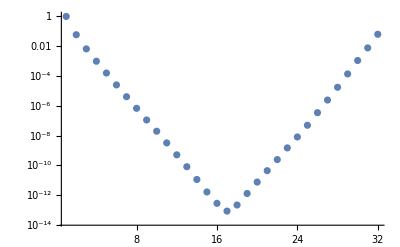

```mathematica
ListLogPlot[datStrγ5Re,PlotRange->All]
```

```mathematica
datStrγ5Re/π2pt
```

{8.41699,9.49636,10.6124,12.5381,15.5228,18.6347,21.9899,26.0024,30.2218,36.657,43.2141,49.7756,55.8045,57.6794,62.2651,71.3227,68.5983,52.5594,46.4928,41.1662,36.5201,30.6231,26.743,23.2133,20.6505,18.5622,16.7049,15.2685,13.9693,12.5883,10.8352,9.56108}

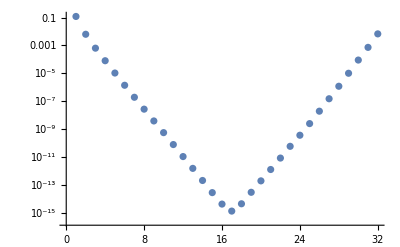

```mathematica
ListLogPlot[π2pt]
```

```mathematica
tags=Import["~//Downloads//comparison//gauge.hdf5"]⟦31⟧
```

/pions/piPlus(all)_piPlus(point(x0y0z0t0))

```mathematica
Evan=Import["~//Downloads//comparison//gauge.hdf5",{"Datasets",tags}];
```

```mathematica
Last/@Total[Evan,{2,4}]
```

{-2.16538×10^-19,5.19127×10^-20,-4.3458×10^-21,5.42496×10^-22,-1.9125×10^-24,-5.74522×10^-24,8.9031×10^-25,3.01175×10^-26,1.95845×10^-26,-1.63955×10^-27,-1.99622×10^-29,-4.38227×10^-30,-2.73079×10^-31,-5.90187×10^-32,8.30212×10^-32,-8.35715×10^-33,1.71233×10^-35,9.93788×10^-34,2.73926×10^-31,-5.07897×10^-31,5.1912×10^-30,-5.11836×10^-29,-5.92845×10^-30,-1.38077×10^-27,-1.94523×10^-26,4.39514×10^-27,-1.05804×10^-24,-2.37563×10^-24,-2.04429×10^-23,7.19351×10^-22,-4.07984×10^-21,-3.67805×10^-20}

```mathematica
πEvan=First/@Total[Evan,{2,4}];
```

```mathematica
πEvan/(8*π2pt)
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00001,0.999992,0.99994,0.999745,0.999883,0.999956,0.999988,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

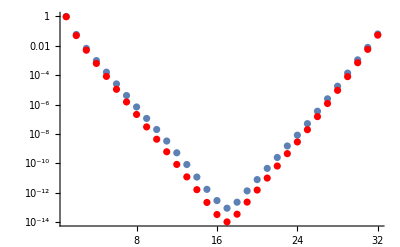

```mathematica
Show[{ListLogPlot[datStrγ5Re],ListLogPlot[8*π2pt,PlotStyle->Red]},PlotRange->All]
```

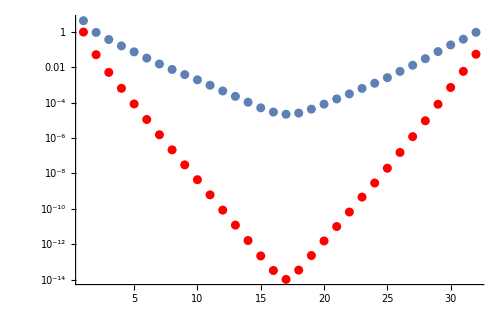

```mathematica
Show[{ListLogPlot[datStrγ5Re],ListLogPlot[πEvan,PlotStyle->Red]},PlotRange->All]
```

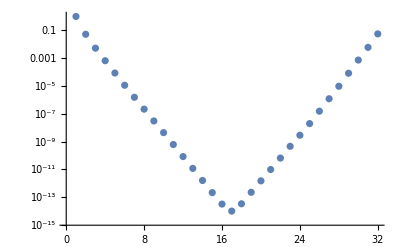

```mathematica
ListLogPlot[First/@Total[Evan,{2,4}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xiaonuxiong/Nustore Files/Nutstore/PDF Euclidean Lattice/Hadron_Structure_Lattice/had_spec

```mathematica
Import["pion_spec.txt","Text"];
```

```mathematica
Table[StringReplace[Import["pion_spec.txt","Text"],{"4 4 4 32"->"32 32 32 96","./wilson_k0.1665_b5.32144_4by32_cfg_4000.lime"->"../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/"<>#}]&[cfgs⟦i⟧],{i,1,Length[cfgs]}]
```

{<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1000.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1001.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1002.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1003.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1004.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1005.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1006.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1007.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1008.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1009.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1010.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1011.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1012.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1013.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1014.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1015.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1016.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1017.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1018.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1019.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1020.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1021.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1022.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <FermionAction>
                        <FermAct>CLOVER</FermAct>
                        <Mass>-0.0743</Mass>
                        <clovCoeffR>1.58932722549812</clovCoeffR>
                        <clovCoeffT>0.902783591772098</clovCoeffT>
                        <AnisoParam>
                            <anisoP>true</anisoP>
                            <t_dir>3</t_dir>
                            <xi_0>4.3</xi_0>
                            <nu>1.265</nu>
                        </AnisoParam>
                        <FermState>
                            <Name>STOUT_FERM_STATE</Name>
                            <rho>0.14</rho>
                            <n_smear>2</n_smear>
                            <orthog_dir>3</orthog_dir>
                            <FermionBC>
                                <FermBC>SIMPLE_FERMBC</FermBC>
                                <boundary>1 1 1 -1</boundary>
                            </FermionBC>
                        </FermState>
                    </FermionAction>
                    <InvertParam>
                        <invType>CG_INVERTER</invType>
                        <RsdCG> 1e-9 </RsdCG>
                        <MaxCG> 100 </MaxCG>
                        <CloverParams>
                            <Mass>-0.0743</Mass>
                            <clovCoeffR>1.58932722549812</clovCoeffR>
                            <clovCoeffT>0.902783591772098</clovCoeffT>
                            <AnisoParam>
                                <anisoP>true</anisoP>
                                <t_dir>3</t_dir>
                                <xi_0>4.3</xi_0>
                                <nu>1.265</nu>
                            </AnisoParam>
                        </CloverParams>
                        <RsdTarget>1.0e-8</RsdTarget>
                        <Delta>0.1</Delta>
                        <MaxIter>10000000</MaxIter>
                        <AntiPeriodicT>true</AntiPeriodicT>
                        <SolverType>BICGSTAB</SolverType>
                        <Verbose>false</Verbose>
                        <AsymmetricLinop>false</AsymmetricLinop>
                        <CudaReconstruct>RECONS_12</CudaReconstruct>
                        <CudaSloppyPrecision>HALF</CudaSloppyPrecision>
                        <CudaSloppyReconstruct>RECONS_12</CudaSloppyReconstruct>
                        <AxialGaugeFix>false</AxialGaugeFix>
                    </InvertParam>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                    <prop_id>pt_prop_1</prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_source_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>Save the prop</annotation>
                <Name>QIO_WRITE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                    <object_type>LatticePropagator</object_type>
                </NamedObject>
                <File>
                    <file_name>./pt_prop_1</file_name>
                    <file_volfmt>SINGLEFILE</file_volfmt>
                </File>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_pt_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>SINK_SMEAR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>5</version>
                    <Sink>
                        <version>2</version>
                        <SinkType>POINT_SINK</SinkType>
                        <j_decay>3</j_decay>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Sink>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <prop_id>pt_prop_1</prop_id>
                    <smeared_prop_id>sh_sh_sink_1</smeared_prop_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation>erase the source to save memory</annotation>
                <Name>ERASE_NAMED_OBJECT</Name>
                <Frequency>1</Frequency>
                <NamedObject>
                    <object_id>pt_prop_1</object_id>
                </NamedObject>
            </elem>
            <elem>
                <annotation> Compute the hadron spectrum. </annotation>
                <Name>HADRON_SPECTRUM</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>1</version>
                    <MesonP>true</MesonP>
                    <CurrentP>false</CurrentP>
                    <BaryonP>false</BaryonP>
                    <time_rev>false</time_rev>
                    <mom2_max>0</mom2_max>
                    <avg_equiv_mom>true</avg_equiv_mom>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <sink_pairs>
                        <elem>
                            <first_id>sh_pt_sink_1</first_id>
                            <second_id>sh_pt_sink_1</second_id>
                        </elem>
                        <elem>
                            <first_id>sh_sh_sink_1</first_id>
                            <second_id>sh_sh_sink_1</second_id>
                        </elem>
                    </sink_pairs>
                </NamedObject>
                <xml_file>hadspec.dat.xml</xml_file>
            </elem>
        </InlineMeasurements>
        <nrow>32 32 32 96</nrow>
    </Param>
    <Cfg>
        <cfg_type>SZINQIO</cfg_type>
        <cfg_file>../../Cnfgrtns/0120-Mpi270-L32-T96/cfg/Mpi270-L32-T96_cfg_1023.lime</cfg_file>
    </Cfg>
</chroma>,<chroma>
    <annotation> Hadron spectrum input </annotation>
    <Param>
        <InlineMeasurements>
            <elem>
                <Name>MAKE_SOURCE</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>6</version>
                    <Source>
                        <version>2</version>
                        <SourceType>POINT_SOURCE</SourceType>
                        <j_decay>3</j_decay>
                        <t_srce>0 0 0 0</t_srce>
                        <SmearingParam>
                            <wvf_kind>GAUGE_INV_GAUSSIAN</wvf_kind>
                            <wvf_param>2.0</wvf_param>
                            <wvfIntPar>5</wvfIntPar>
                            <no_smear_dir>3</no_smear_dir>
                        </SmearingParam>
                    </Source>
                </Param>
                <NamedObject>
                    <gauge_id>default_gauge_field</gauge_id>
                    <source_id>pt_source_1</source_id>
                </NamedObject>
            </elem>
            <elem>
                <Name>PROPAGATOR</Name>
                <Frequency>1</Frequency>
                <Param>
                    <version>10</version>
                    <quarkSpinType>FULL</quarkSpinType>
                    <obsvP>false</obsvP>
                    <